```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

```mathematica
FitError[func_,list_,p_]:=Module[{tab1,nbin},
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}];
If[p==Null,
tab1=Table[(list[[i,2]]-func[list[[i,1]]])^2,{i,1,Length[list]}],
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}]
];
nbin=Length[tab1];
√(Total[tab1]/(nbin-1))
]
```

```mathematica
ResidualSum[func_,P_,param_]:=Module[{tab1,nbin,Ntot,dbin},
Ntot=Total[P[[All,2]]];
dbin=P[[2,1]]-P[[1,1]];
tab1=Table[(P[[i,2]]- func[P[[i,1]],param])^2,{i,1,Length[P]}];
Total[tab1]
]
```

```mathematica
ChiSqr[func_,hist_,p_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=hist[[2,1]]-hist[[1,1]];
Ntot=Total[hist[[All,2]]];
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]],p])^2/(Ntot dbin  func[hist[[i,1]],p]),{i,1,Length[hist]}];
If[p== Null,
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]]])^2/(Ntot dbin  func[hist[[i,1]]]),{i,1,Length[hist]}]
];
nbin=Length[hist];
Total[tab1]
]
RedChiSqr[func_,hist_,p_]:=ChiSqr[func,hist,p]/(Length[hist]-1);
```

```mathematica
SemiPoisson[s_]:=4 s Exp[-2 s]
```

```mathematica
porterthomas[x_]:=Exp[-x/2]/(√(2π x))
```

```mathematica
genpt[x_,ν_]:=(ν/2 x)^(ν/2-1)/Gamma[ν/2] ν/2 Exp[-ν/2 x]
```

```mathematica
GenPTDistribution=ProbabilityDistribution[genpt[x,ν],{x,0,∞},Assumptions->ν>0]
```

ProbabilityDistribution[(2^(-ν/2) ⅇ^(-(x ν)/2) ν (x ν)^(-1+ν/2))/Gamma[ν/2],{x,0,∞},Assumptions→ν>0]

```mathematica
genpt[x,1]
```

ⅇ^(-x/2)/(√(2 π) √x)

```mathematica
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
WidthData[ic_,E1_,E2_]:=Select[AWD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
Select[AWD,(#1[[7]]>10^-1)&]*)
```

```mathematica
iens=1;icoup=1;
```

```mathematica
path1=StringJoin[{"~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.",ToString[iens*1000+icoup]}]
(*path1=StringJoin[{"~/Code/Nchannel/Square/CODES/fort.",ToString[iens*1000+icoup]}]*)
```

~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.1001

```mathematica
Data=DeleteCases[Import[path1,"Table"],{}];
```

```mathematica
iemax=Length[Data];iemin=1;
sigma=Table[{Data[[ie,2]],Data[[ie,10]]},{ie,iemin,iemax}];
lzclose=Table[{Data[[ie,2]], Log[Data[[ie,6]]]},{ie,iemin,iemax}];
alsqr=Table[{Data[[ie,2]],Data[[ie,5]]},{ie,iemin,iemax}];
albgsqr=Table[{Data[[ie,2]],Sin[Data[[ie,8]]]^2},{ie,iemin,iemax}];
phaseopi=Table[{Data[[ie,2]],Data[[ie,11]]},{ie,iemin,iemax}];
ltimedelay=Table[{Data[[ie,2]],Log[Data[[ie,12]]]},{ie,iemin,iemax}];
ascat = Table[{Data[[ie,2]],Data[[ie,4]]},{ie,iemin,iemax}];
abg=  Table[{Data[[ie,2]],Data[[ie,13]]},{ie,iemin,iemax}];
BSdet = Table[{Data[[ie,2]],Data[[ie,7]]},{ie,iemin,iemax}];
```

```mathematica
padding={{100,45},{80,0}};
imgsize={600,300};
yrange=All;
xrange={0,0.1};
aspctratio=Full;1/GoldenRatio;
pabg=ListPlot[abg,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a_bg/r_0"},LabelStyle->{16},PlotRange->{xrange,{-1000,1000}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
palsqr=ListPlot[{alsqr,albgsqr},Joined->True,PlotStyle->{{Black},{Red,Dotted}},Frame->True,FrameLabel->{"E/(ℏ^2/2μ r_0^2)",TraditionalForm[Sin[δ]^2]},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio,FrameTicks->{Automatic,Automatic}];
psigma=ListPlot[sigma,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","σ/r_0^2"},LabelStyle->{16},PlotRange->{xrange,yrange},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
pstair=ListPlot[phaseopi,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","δ_0/π"},LabelStyle->{16},PlotRange->{xrange,All},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
plzc=ListPlot[lzclose,Joined->True,PlotStyle->{Red,Dashed},Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","log(Z_C)"},LabelStyle->{16},PlotRange->{xrange,{-7,18}},GridLines->Automatic,ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pltd=ListPlot[ltimedelay,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{(*"E/(ℏ^2/2μr_0^2)"*)None,TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)]]},LabelStyle->Large,PlotRange->{xrange,{-7,18}},GridLines->Automatic,FrameTicks->{Automatic,Automatic},ImageSize->{600,250},ImagePadding->{{100,45},{8,8}},AspectRatio->aspctratio,ImageMargins->0,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}}];
pascat=ListPlot[ascat,Joined->True,PlotStyle->Black,Frame->True,FrameLabel->{"E/(ℏ^2/2μr_0^2)","a/r_0"},LabelStyle->{16},PlotRange->{xrange,{-100,100}},GridLines->Automatic,ImageSize->imgsize,ImagePadding->padding,AspectRatio->aspctratio];
```

```mathematica
pbsdet=ListPlot[BSdet,Joined->True,PlotStyle->Black,Frame->True,LabelStyle->{16},PlotRange->{xrange,{-10^-100,10^-100}},AspectRatio->50/1000,ImageSize->{600,50},PlotRangeClipping->False,ImagePadding->{{100,45},{0,20}},FrameTicks->{None,None},ImageMargins->0,Axes->False,Epilog->{Text[Style["(a)",Bold,22],{-0.015,0}]}]
```

-Graphics-

```mathematica
AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/end-cases/fort.800","Table"],{}];
(*AllResData=DeleteCases[Import["~/Code/Nchannel/Square/CODES/fort.800","Table"],{}];*)
ResData[iens_,icoup_]:=Select[Select[AllResData,(#[[2]]==iens)&],(#[[3]]==icoup)&]
Resonances = ResData[iens,icoup];
NumRes=Length[Resonances];

ResLines=Table[ssbg  (EE-ER+q Γ/2)^2/((EE-ER)^2+(Γ/2)^2)/.{ssbg->Resonances[[ires,9]],ER->Resonances[[ires,5]],Γ->Resonances[[ires,7]],q->Resonances[[ires,8]]},{ires,1,NumRes}];
resplots=Table[Plot[Evaluate[ResLines[[ires]]],{EE,Resonances[[ires,5]]-2Resonances[[ires,7]],Resonances[[ires,5]]+2Resonances[[ires,7]]},PlotStyle->{Blue,Dashed},PlotRange->All,ImagePadding->padding,ImageSize->imgsize,AspectRatio->Full],{ires,1,NumRes}];
```

```mathematica
widthdata=Table[{Resonances[[ires,5]],Resonances[[ires,7]]},{ires,1,NumRes}];
qdata=Table[{Resonances[[ires,5]],Resonances[[ires,8]]},{ires,1,NumRes}];
```

```mathematica
pwidth=ListPlot[widthdata,PlotStyle->Black,Frame->True,LabelStyle->Medium,FrameLabel->{"E","Γ/(ℏ^2/2μr_0^2)"}];
```

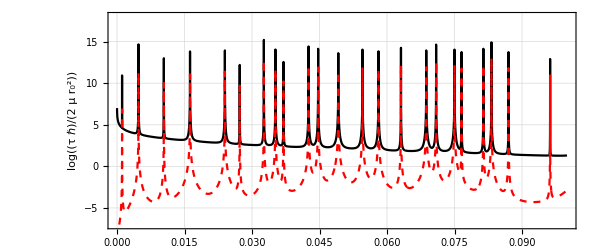

```mathematica
ptdlz=Show[{pltd,plzc},PlotRange->{xrange,{-7,18}},FrameLabel->{{TraditionalForm[Log[(τ ℏ)/(2μ Subscript[r, 0]^2)] ],TraditionalForm[Style[Log[Subscript[Z, C]],Red]]},{None,None}},PlotRangeClipping->False,Epilog->{Text[Style["(b)",Bold,22],{-.015,15.}]}]
```

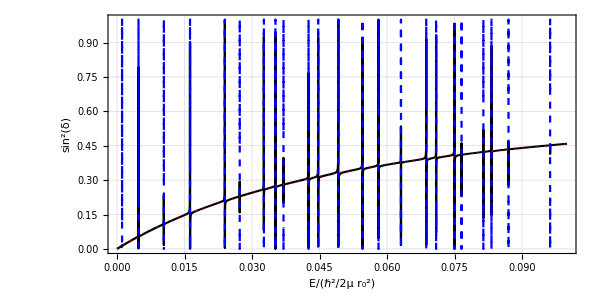

```mathematica
pfanolines = Show[{palsqr,resplots},PlotRange->{xrange,{0,1}},LabelStyle->Large,PlotRangeClipping->False,Epilog->{Text[Style["(c)",Bold,22],{-.015,0.9}]}]
```

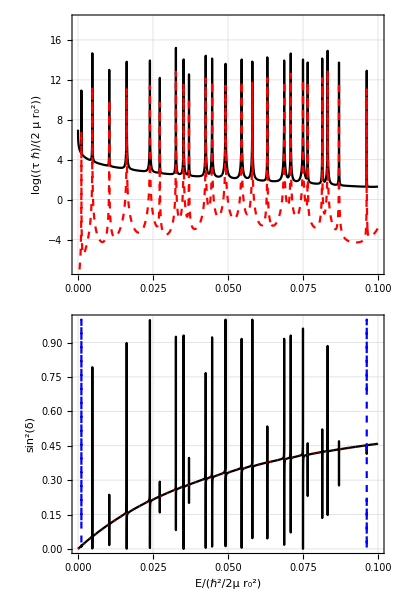

```mathematica
p1=Grid[{{pbsdet},{ptdlz},{pfanolines}},Spacings->0]
```

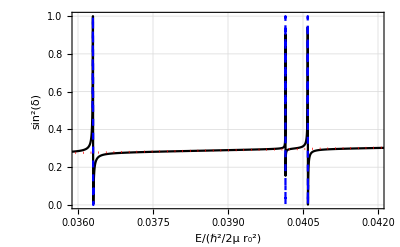

```mathematica
pfanofits=Show[pfanolines,PlotRange->{{0.036,0.042},All},ImagePadding->Automatic,ImageSize->Automatic,AspectRatio->1/GoldenRatio,PlotRangeClipping->True]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf",pfanofits]
```

~/Code/Nchannel/Square/CODES/plots/p-fanofits.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-poisson-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-wigner-scat.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf",p1]
```

~/Code/Nchannel/Square/CODES/plots/p-tridiag-chris-3chan-scat.pdf

### Statistical Data

```mathematica
AllResonanceData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
```

```mathematica
ARD=DeleteCases[DeleteCases[AllResonanceData,AllResonanceData[[1]]],{}];
```

```mathematica
DataSelect[ic_,E1_,E2_]:=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
```

```mathematica
ic=1;
Emin=0.0;Emax=0.1;
DataSubset=DataSelect[ic,Emin,Emax];
```

```mathematica
Select[DataSubset,(#1[[7]]>10^-1)&]
```

{}

```mathematica
bins=Join[Table[x,{x,0,3,0.05}],Table[x,{x,3.25,5,0.25}]];
bfit=Table[0.5(bins[[i]]+bins[[i+1]]),{i,1,Length[bins]-1}]
```

{0.025,0.075,0.125,0.175,0.225,0.275,0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975,1.025,1.075,1.125,1.175,1.225,1.275,1.325,1.375,1.425,1.475,1.525,1.575,1.625,1.675,1.725,1.775,1.825,1.875,1.925,1.975,2.025,2.075,2.125,2.175,2.225,2.275,2.325,2.375,2.425,2.475,2.525,2.575,2.625,2.675,2.725,2.775,2.825,2.875,2.925,2.975,3.125,3.375,3.625,3.875,4.125,4.375,4.625,4.875}

```mathematica
SummaryData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];
(*Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];*)
SD=DeleteCases[SummaryData,SummaryData[[1]]];
```

```mathematica
nw=Length[DataSubset]
```

3993

```mathematica
WidthArray=Table[DataSubset[[i,7]]/(√DataSubset[[i,5]]),{i,1,nw}];
```

```mathematica
MeanWidth=Mean[WidthArray]
```

4.64732×10^-6

```mathematica
Median[WidthArray]
```

2.0749×10^-6

```mathematica
ScaledWidths=WidthArray/MeanWidth;
```

```mathematica
WidthBinCounts1=BinCounts[ScaledWidths,{bins}];
```

```mathematica
NormalizedWidthHistogram=Table[{bins[[i]],WidthBinCounts1[[i]]/nw/(bins[[i+1]]-bins[[i]])},{i,1,Length[bins]-1}];
```

```mathematica
Widthσi=1/(√WidthBinCounts1[[All]])
```

{1/(11 √6),1/(√271),1/(√218),1/(√178),1/(2 √37),1/(√109),1/(√110),1/(√133),1/(√111),1/10,1/(√95),1/(5 √3),1/(√85),1/(√59),1/(√57),1/(√70),1/(√65),1/(3 √6),1/(√55),1/(5 √2),1/(√43),1/(√47),1/(√41),1/(3 √5),1/(√41),1/(√35),1/(4 √2),1/(√43),1/(√29),1/(√43),1/(2 √7),1/(√21),1/(√22),1/5,1/(√30),1/(2 √6),1/(3 √3),1/(2 √7),1/(√19),1/5,1/(√19),1/(2 √6),1/(2 √3),1/(√19),1/(√14),1/(√19),1/(√11),1/(√14),1/(2 √2),1/(√14),1/(√14),1/(√15),1/3,1/(√7),1/3,1/(√10),1/(√11),1/(√2),1/3,1/(√11),1/(4 √2),1/(√42),1/5,1/(2 √6),1/(4 √2),1/(3 √2),1/(√17),1/(√13)}

```mathematica
WidthWeights=1/Widthσi[[All]]^2
```

{726,271,218,178,148,109,110,133,111,100,95,75,85,59,57,70,65,54,55,50,43,47,41,45,41,35,32,43,29,43,28,21,22,25,30,24,27,28,19,25,19,24,12,19,14,19,11,14,8,14,14,15,9,7,9,10,11,2,9,11,32,42,25,24,32,18,17,13}

```mathematica
nw
```

3993

```mathematica
Total[WidthWeights]
```

3871

```mathematica
genpt[x,ν]
```

(2^(-ν/2) ⅇ^(-(x ν)/2) ν (x ν)^(-1+ν/2))/Gamma[ν/2]

```mathematica
FitWidthHistogram=Table[{bfit[[i]],WidthBinCounts1[[i]]/nw/(bins[[i+1]]-bins[[i]])},{i,1,Length[bfit]}]
```

{{0.025,3.63636},{0.075,1.35738},{0.125,1.09191},{0.175,0.89156},{0.225,0.741297},{0.275,0.545955},{0.325,0.550964},{0.375,0.666166},{0.425,0.555973},{0.475,0.500877},{0.525,0.475833},{0.575,0.375657},{0.625,0.425745},{0.675,0.295517},{0.725,0.2855},{0.775,0.350614},{0.825,0.32557},{0.875,0.270473},{0.925,0.275482},{0.975,0.250438},{1.025,0.215377},{1.075,0.235412},{1.125,0.205359},{1.175,0.225394},{1.225,0.205359},{1.275,0.175307},{1.325,0.16028},{1.375,0.215377},{1.425,0.145254},{1.475,0.215377},{1.525,0.140245},{1.575,0.105184},{1.625,0.110193},{1.675,0.125219},{1.725,0.150263},{1.775,0.12021},{1.825,0.135237},{1.875,0.140245},{1.925,0.0951665},{1.975,0.125219},{2.025,0.0951665},{2.075,0.12021},{2.125,0.0601052},{2.175,0.0951665},{2.225,0.0701227},{2.275,0.0951665},{2.325,0.0550964},{2.375,0.0701227},{2.425,0.0400701},{2.475,0.0701227},{2.525,0.0701227},{2.575,0.0751315},{2.625,0.0450789},{2.675,0.0350614},{2.725,0.0450789},{2.775,0.0500877},{2.825,0.0550964},{2.875,0.0100175},{2.925,0.0450789},{2.975,0.0550964},{3.125,0.0320561},{3.375,0.0420736},{3.625,0.0250438},{3.875,0.0240421},{4.125,0.0320561},{4.375,0.0180316},{4.625,0.0170298},{4.875,0.0130228}}

```mathematica
Total[FitWidthHistogram[[All,2]]]
```

18.5755

```mathematica
Length[FitWidthHistogram]
```

68

```mathematica
ν0=0.5;
ph=ListPlot[NormalizedWidthHistogram,PlotRange->All,InterpolationOrder->0,Joined->True,PlotStyle->Black];
(*w1nlm=FindFit[FitWidthHistogram,{genpt[γ,ν]},{{ν,1.0}},γ]*)
w1nlm=NonlinearModelFit[FitWidthHistogram,genpt[γ,ν],{ν},γ,Method->"LevenbergMarquardt"]
pgenpt=Plot[genpt[γ,ν/.w1nlm["BestFitParameters"]],{γ,0,5},PlotStyle->{Red},PlotRange->All];
```

FittedModel[(0.257355 ⅇ^(-0.331467 γ))/γ^0.668533]

```mathematica
NumberForm[ν/.w1nlm["BestFitParameters"],{6,4}]
```

0.6629

```mathematica
w1nlm["BestFitParameters"]
```

{ν→0.662935}

```mathematica
√(2(D[ChiSqr[genpt,FitWidthHistogram,ν],{ν,2}]/.w1nlm["BestFitParameters"])^-1)
```

0.222994

```mathematica
w1nlm["ParameterErrors"]
```

{0.0547745}

```mathematica
Total[w1nlm["FitResiduals"]^2]
```

0.666325

```mathematica
ChiSqr[genpt,FitWidthHistogram,1.]
```

1.16722

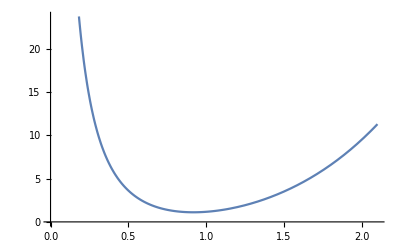

```mathematica
Plot[ChiSqr[genpt,FitWidthHistogram,ν],{ν,0.0,2.1}]
```

```mathematica
w1nlm["ParameterErrors"]
```

{0.0547745}

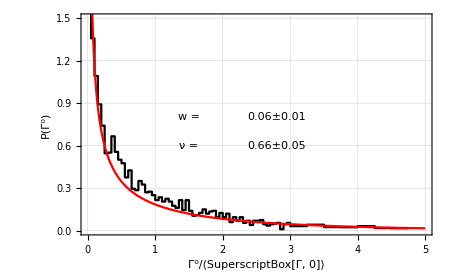

```mathematica
pporterthomas=Show[{ph,pgenpt},PlotRange->{0,1.5},Frame->True,GridLines->Automatic,FrameLabel->{"Γ^0/⟨SuperscriptBox[Γ, 0]⟩","P(Γ^0)"},LabelStyle->Large,Epilog->{
Text[Style["w = ",Large],{1.5,0.8}],
Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{2.8,0.8}],
Text[Style["ν = ",Large],{1.5,0.6}],Text[Style[NumberForm[ν/.w1nlm["BestFitParameters"],{3,2}]±NumberForm[w1nlm["ParameterErrors"][[1]],{3,2}],Large],{2.8,0.6}](*,
Text[Style["SE_PT = ",Large],{2.6,0.4}],
Text[Style[NumberForm[FitError[porterthomas,wcfit,Null],{3,2}],Large],{3.7,0.4}],*)
(*Text[Style["SE_ad = ",Large],{2.0,0.2}],*)
}]
```

### Distribution for the time delay

```mathematica
Integrate[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,∞}]
```

1

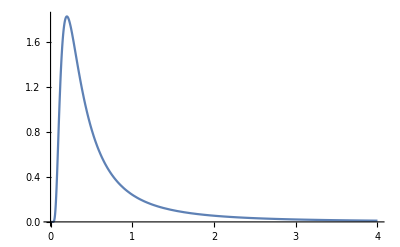

```mathematica
Plot[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,4},PlotRange->All]
```

```mathematica
ic=1;
WDtest=Select[AWD,(#1[[3]]==ic)&];
```

```mathematica
nw=Length[WDtest]
```

3996

```mathematica
tdarray=Table[4/WDtest[[i,7]],{i,1,nw}];
```

```mathematica
tdarray[[1]]
```

859328.

```mathematica
meantd=Mean[tdarray]
```

2.13676×10^8

```mathematica
Median[tdarray]
```

469528.

```mathematica
{Min[tdarray],Max[tdarray]}
```

{6622.52,3.02755×10^11}

```mathematica
dtb=0.1;tbins=Table[i,{i,0,4,dtb}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
tbinfit=Table[(tbins[[i]]+tbins[[i+1]])/2,{i,1,Length[tbins]-1}]
```

{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95}

```mathematica
td1=BinCounts[tdarray/meantd,{tbins}]
```

{3684,94,37,30,22,8,16,11,7,3,2,2,0,3,6,2,4,1,2,3,5,4,2,2,1,0,0,0,0,0,4,1,1,2,2,0,0,0,0,0}

```mathematica
tdfit=Table[{tbinfit[[i]],td1[[i]]/nw/dtb},{i,1,Length[wcnorm]}];
```

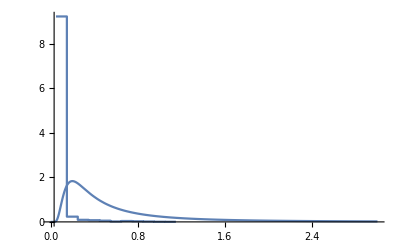

```mathematica
Show[{ListPlot[tdfit,InterpolationOrder->0,Joined->True,PlotRange->All],Plot[(1/2)^(M/2)Exp[-M /(2τ)]/(Gamma[M/2](M τ)^((M+4)/2))/.M->1,{τ,0,3}]},PlotRange->All]
```

Well... that doesn’t seem right at all.

### Zclose vs. width

```mathematica
Scaledgammazc[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWDTrimmed,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,7]]/√WidthData[[i,5]],WidthData[[i,6]]},{i,1,nw}]
]
```

```mathematica
gammazc[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWDTrimmed,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,7]],WidthData[[i,6]]},{i,1,nw}]
]
```

```mathematica
Length[ARD]
```

163128

```mathematica
ScaledAllgammazc=Table[{ARD[[i,7]]/√ARD[[i,5]],ARD[[i,6]]},{i,1,Length[ARD]}];
```

```mathematica
Allgammazc=Table[{ARD[[i,7]],ARD[[i,6]]},{i,1,Length[ARD]}];
```

```mathematica
punscaledgammazc=Show[{ListLogLogPlot[Allgammazc,PlotRange->{{10^-13,10^-3},{10^3,10^13}},Frame->True,LabelStyle->{12},PlotMarkers->{"●",1.0},PlotStyle->{Small,Black},FrameLabel->{TraditionalForm["Γ^0"/"√(ℏ^2)"],TraditionalForm[Subscript[Z, C]]},ImageSize->{500,500/1.6}],LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-13,10^-0},PlotStyle->{Red,Dashed,Thin}]}];
```

```mathematica
pgammazc=Show[{ListLogLogPlot[ScaledAllgammazc,PlotRange->{{10^-13,10^-0},{10^3,10^13}},Frame->True,LabelStyle->{Large},PlotMarkers->{"●",1.0},PlotStyle->{Small,Black},FrameLabel->{TraditionalForm["Γ^0"/"√(ℏ^2)"],TraditionalForm[Subscript[Z, C]]},ImageSize->{700,700/1.6}],LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-13,10^-0},PlotStyle->{Red,Dashed,Thin}]},Epilog->{Inset[punscaledgammazc,ImageScaled[{0.5,0.4}],ImageScaled[{0,0}],ImageScaled[{.48,.56}]]}];
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pgammazc.png",pgammazc]
```

~/Code/Nchannel/Square/CODES/plots/pgammazc.png

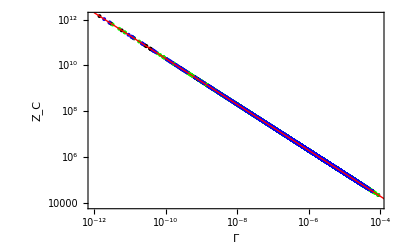

```mathematica
Show[{ListLogLogPlot[{gammazc[1,0.0,0.1],gammazc[10,0.0,0.1],gammazc[50,0.0,0.1]},Frame->True,LabelStyle->Large,PlotMarkers->{"●",4.0},PlotStyle->{{Small,Black},{Small,Green},{Small,Blue}},FrameLabel->{TraditionalForm[Γ],TraditionalForm[Subscript[Z, C]]}],
(*ListLogLogPlot[gammazc[2],Frame->True,LabelStyle->Large,PlotMarkers->{"●",2.0},PlotStyle->{Small,Blue},FrameLabel->{TraditionalForm[Γ],TraditionalForm[Subscript[Z, C]]}],*)
LogLogPlot[A (x)^b/.{A->2,b->-1},{x,10^-12,10^1},PlotStyle->{Red,Thin}]}]
```

```mathematica
Spoles[ic_,E1_,E2_]:=Module[{WidthData,i,nw},
WidthData=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];(*Select[AWD,(#1[[3]]==ic )&];*)
nw=Length[WidthData];
Table[{WidthData[[i,5]],WidthData[[i,7]]/(√WidthData[[i,5]])},{i,1,nw}]
]
```

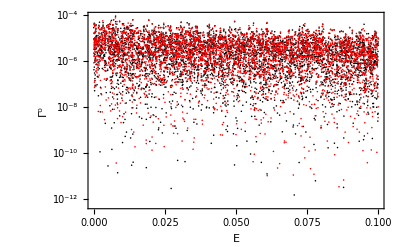

```mathematica
Dom={0.0,0.1};ListLogPlot[{Spoles[1,Dom[[1]],Dom[[2]]],Spoles[2,Dom[[1]],Dom[[2]]]},Frame->True,LabelStyle->Large,PlotStyle->{{Black,Small},{Red,Small}},FrameLabel->{TraditionalForm["E"],TraditionalForm["Γ^0"]},PlotRange->{Dom,All}]
```

### Level Spacings with Mathematica

```mathematica
genpt[x_,ν_]:=(ν/2 x)^(ν/2-1)/Gamma[ν/2] ν/2 Exp[-ν/2 x]
```

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
```

```mathematica
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

```mathematica
SemiPoisson[s_]:=4 s Exp[-2 s]
```

```mathematica
porterthomas[x_]:=Exp[-x/2]/(√(2π x))
```

```mathematica
GenPTDistribution=ProbabilityDistribution[genpt[x,ν],{x,0,∞},Assumptions->ν>0]
```

ProbabilityDistribution[(2^(-ν/2) ⅇ^(-(x ν)/2) ν (x ν)^(-1+ν/2))/Gamma[ν/2],{x,0,∞},Assumptions→ν>0]

```mathematica
AllResonanceData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
ARD=DeleteCases[DeleteCases[AllResonanceData,AllResonanceData[[1]]],{}];
DataSelect[ic_,E1_,E2_]:=Select[ARD,(#1[[3]]==ic && E1<#1[[5]]<E2)&];
```

```mathematica
LevelSpacings[ic_,nens_,ARD_]:=Module[{datatemp,nr,ls,iens},
datatemp=Table[Select[ARD,(#1[[3]]==ic && #1[[2]]==iens)&],{iens,1,nens}];
nr=Table[Length[datatemp[[iens]]],{iens,1,nens}];
ls=Table[Table[datatemp[[iens,i+1,5]]-datatemp[[iens,i,5]],{i,1,nr[[iens]]-1}],{iens,1,nens}];
ls=Flatten[ls];
ls = ls/Mean[ls]
]
```

```mathematica
(*ls=Table[LevelSpacings[ic,100,ARD],{ic,1,50}];*)
```

```mathematica
(*Export["~/Code/Nchannel/Square/CODES/plots/linespacings.dat",ls]*)
```

~/Code/Nchannel/Square/CODES/plots/linespacings.dat

```mathematica
ls=Import["~/Code/Nchannel/Square/CODES/plots/linespacings.dat","Table"];
```

```mathematica
r1=Table[FindDistributionParameters[ls[[ic]],BrodyDistribution],{ic,1,50}]
```

{{w→0.0499654},{w→0.12031},{w→0.192342},{w→0.255456},{w→0.312029},{w→0.367889},{w→0.416437},{w→0.461146},{w→0.507934},{w→0.551645},{w→0.58677},{w→0.627763},{w→0.665902},{w→0.69149},{w→0.714167},{w→0.735682},{w→0.748762},{w→0.769472},{w→0.791131},{w→0.803094},{w→0.818632},{w→0.835699},{w→0.847166},{w→0.860136},{w→0.870283},{w→0.879756},{w→0.890347},{w→0.89366},{w→0.90458},{w→0.899762},{w→0.905678},{w→0.90589},{w→0.897901},{w→0.894926},{w→0.890297},{w→0.88223},{w→0.883776},{w→0.883657},{w→0.885711},{w→0.893603},{w→0.900819},{w→0.911948},{w→0.920108},{w→0.925237},{w→0.931174},{w→0.939581},{w→0.947278},{w→0.951065},{w→0.950262},{w→0.955276}}

```mathematica
NewBrodyBC=Table[BinCounts[ls[[ic]],{bins}],{ic,1,50}];
NormalizedBrodyBC=Table[Table[NewBrodyBC[[ic,i]]/Total[NewBrodyBC[[ic]]]/(bins[[i+1]]-bins[[i]]),{i,1,Length[bins]-1}],{ic,1,50}];
```

```mathematica
NewBrodyPDist=Table[Table[{bfit[[i]],NormalizedBrodyBC[[ic,i]]},{i,1,Length[bfit]}],{ic,1,50}];
```

```mathematica
BrodyFitNLM=Table[NonlinearModelFit[NewBrodyPDist[[ic]],PBrody[z,w],{w},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9999],{ic,1,50}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

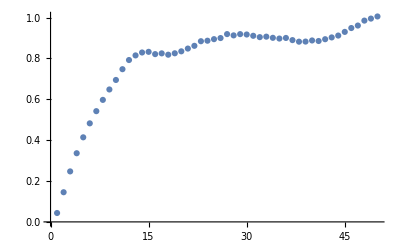

```mathematica
ListPlot[w/.Table[BrodyFitNLM[[ic]]["BestFitParameters"],{ic,1,50}]]
```

```mathematica
brodydata=Table[{SD[[ic,5]],w/.BrodyFitNLM[[ic]]["BestFitParameters"]},{ic,1,Length[SD]}];
brodyfiterror=Table[BrodyFitNLM[[ic]]["ParameterErrors"][[1]],{ic,1,Length[SD]}];
brodydatap=Table[{brodydata[[ic,1]],brodydata[[ic,2]]+brodyfiterror[[ic]]},{ic,1,Length[SD]}];
brodydatam=Table[{brodydata[[ic,1]],brodydata[[ic,2]]-brodyfiterror[[ic]]},{ic,1,Length[SD]}];
```

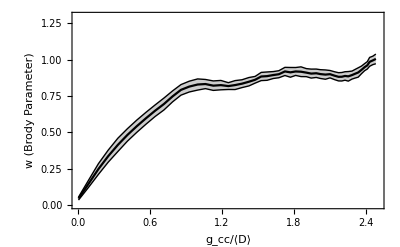

```mathematica
pbrody1=ListPlot[{brodydatam,brodydata,brodydatap},Frame->True,PlotStyle->{{Black,Thin},{Black},{Black,Thin}},Filling->{1->{3}},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","w (Brody Parameter)"},GridLines->None,PlotRange->{{0,2.5},{0,1.3}},Epilog->{Inset[pgocplot,{1.6,.37},{Automatic,Automatic},{1.4,0.7}]}]
```

### Level Spacing data from fortran

```mathematica
PSdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.500","Table"];(*Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];*)
PSD=DeleteCases[PSdat,PSdat[[1]]];
```

```mathematica
Length[PSD]
```

50

```mathematica
sbc=Table[Table[{bins[[i]],PSD[[ic,i+8]]},{i,1,20}],{ic,1,Length[PSD]}];
sbnorm=Table[Table[{bins[[i]],sbc[[ic,i,2]]},{i,1,Length[bins]-1}],{ic,1,Length[PSD]}];
SBinFitArray=Table[Table[{(bins[[i]]+bins[[i+1]])/2,sbc[[ic,i,2]]},{i,1,Length[bins]-1}],{ic,1,Length[PSD]}];
```

```mathematica
w0=0.5;
```

```mathematica
ph=Table[ListPlot[sbnorm[[ic]],InterpolationOrder->0,Joined->True,PlotStyle->Black],{ic,1,Length[PSD]}];
```

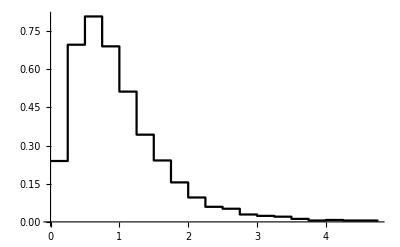

```mathematica
ph[[10]]
```

```mathematica
psp=Plot[4s Exp[-2s],{s,0,5},PlotStyle->{Blue,Dashed}];
```

```mathematica
NonlinearModelFit[SBinFitArray[[1]],PBrody[z,w],{w},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9999]
```

FittedModel[1.03263 ⅇ^(-0.977325 z^1.05659) z^0.0565872]

```mathematica
nlmbrody=Table[NonlinearModelFit[SBinFitArray[[ic]],PBrody[z,w],{w},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9999],{ic,1,Length[PSD]}];
pb=Table[Plot[PBrody[z,w/.nlmbrody[[ic]]["BestFitParameters"]],{z,0,5},PlotStyle->{Red}],{ic,1,Length[PSD]}];
```

```mathematica
nlmbrody[[10]]["ParameterErrors"][[1]]
```

0.0606595

```mathematica
gocdata=Table[{SD[[i,5]],SD[[i,4]]},{i,1,Length[SD]}];
```

```mathematica
brodydata=Table[{PSD[[ic,5]],w/.nlmbrody[[ic]]["BestFitParameters"]},{ic,1,Length[PSD]}];
```

```mathematica
brodyfiterror=Table[nlmbrody[[ic]]["ParameterErrors"][[1]],{ic,1,Length[PSD]}];
```

```mathematica
brodydatap=Table[{brodydata[[ic,1]],brodydata[[ic,2]]+brodyfiterror[[ic]]},{ic,1,Length[PSD]}];
brodydatam=Table[{brodydata[[ic,1]],brodydata[[ic,2]]-brodyfiterror[[ic]]},{ic,1,Length[PSD]}];
```

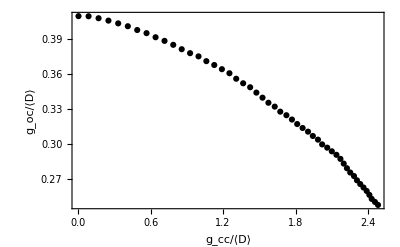

```mathematica
pgocplot=ListPlot[gocdata,PlotStyle->Black,Frame->True,FrameLabel->{"g_cc/⟨D⟩","g_oc/⟨D⟩"},LabelStyle->{12}]
```

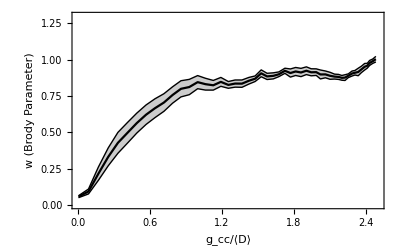

```mathematica
pbrody1=ListPlot[{brodydatam,brodydata,brodydatap},Frame->True,PlotStyle->{{Black,Thin},{Black},{Black,Thin}},Filling->{1->{3}},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","w (Brody Parameter)"},GridLines->None,PlotRange->{{0,2.5},{0,1.3}},Epilog->{Inset[pgocplot,{1.6,.37},{Automatic,Automatic},{1.4,0.7}]}]
```

```mathematica
Show[pbrody1]
```

-Graphics-

```mathematica
DataArray=Table[DataSelect[ic,0,0.1],{ic,1,Length[SD]}];
```

```mathematica
nw=Table[Length[DataArray[[ic]]],{ic,1,Length[SD]}];
```

```mathematica
nw
```

{3993,3994,3978,3964,3947,3923,3898,3872,3846,3815,3790,3764,3728,3683,3656,3612,3582,3547,3514,3476,3437,3402,3373,3311,3278,3249,3214,3174,3141,3108,3057,3026,2985,2948,2917,2884,2856,2820,2797,2771,2735,2694,2661,2632,2588,2552,2530,2504,2470,2432}

```mathematica
WidthArrayTemp=Table[Table[DataArray[[ic]][[i,7]],{i,1,nw[[ic]]}],{ic,1,Length[SD]}];
```

```mathematica
MeanWidth=Table[Mean[WidthArrayTemp[[ic]]],{ic,1,Length[SD]}];
```

```mathematica
ScaledWidthArray=Table[WidthArrayTemp[[ic]]/MeanWidth[[ic]],{ic,1,Length[SD]}];
```

```mathematica
WidthCountsTemp=Table[BinCounts[ScaledWidthArray[[ic]],{bins}],{ic,1,Length[SD]}];
```

```mathematica
WidthCountsTemp[[1]]
```

{704,291,211,177,142,133,115,104,90,96,85,92,85,64,62,52,67,65,52,42,47,43,46,49,46,41,30,34,36,24,27,28,26,27,23,13,30,26,29,22,16,9,25,17,26,21,17,19,10,12,18,13,19,11,15,7,17,10,8,8,54,36,20,29,24,13,15,14}

```mathematica
WidthHistograms=Table[Table[{(bins[[i]]+bins[[i+1]])/2,WidthCountsTemp[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,Length[SD]}];
```

```mathematica
NormalizedWidthHistTemp=Table[Table[{bins[[i]],WidthCountsTemp[[ic,i]]/nw[[ic]]/(bins[[i+1]]-bins[[i]])},{i,1,Length[bins]-1}],{ic,1,Length[SD]}];
```

```mathematica
Length[NormalizedWidthHistTemp]
```

50

```mathematica
WidthFitHist=Table[Table[{bfit[[i]],NormalizedWidthHistTemp[[ic,i,2]]},{i,1,Length[bfit]}],{ic,1,Length[SD]}];
```

```mathematica
Widthnlm=Table[NonlinearModelFit[WidthFitHist[[ic]],{genpt[γ,ν]},{{ν,1.0}},γ,Method->Automatic],{ic,1,Length[SD]}];
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

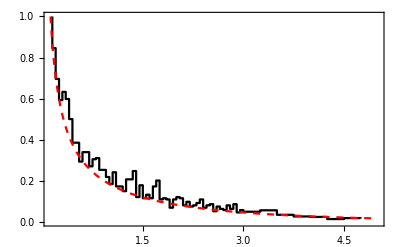

```mathematica
ic=20;ppt1=Show[ListPlot[NormalizedWidthHistTemp[[ic]],Joined->True,InterpolationOrder->0,PlotRange->{0,1},Frame->True,PlotStyle->Black,LabelStyle->Large],Plot[genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],{γ,0,5},PlotRange->{0,1},PlotStyle->{Red,Dashed}],PlotRange->{0,1}]
```

```mathematica
√(Widthnlm[[1]]["CovarianceMatrix"])
```

{{0.0463855}}

```mathematica
Widthnlm[[1]]["ParameterErrors"]
```

{0.0463855}

```mathematica
SD[[1]]
```

{1,1,0.0024445,0.40909,0.0040909,0.00035698,0.055357,0.0084496}

```mathematica
histnufittable=Table[{SD[[ic,5]],ν/.FindDistributionParameters[ScaledWidthArray[[ic]],GenPTDistribution]},{ic,1,Length[SD]}]
```

{{0.0040909,1.00774},{0.087476,1.00398},{0.17015,1.00882},{0.25192,1.0055},{0.3326,0.987513},{0.41224,1.00225},{0.48993,0.993892},{0.56708,0.994921},{0.6418,0.997012},{0.71583,0.996165},{0.78805,0.976069},{0.85805,0.974295},{0.92742,0.969758},{0.99716,0.960355},{1.0619,0.958158},{1.1274,0.959052},{1.1906,0.940737},{1.2529,0.965387},{1.309,0.980952},{1.3665,0.989723},{1.4244,0.995564},{1.4759,0.986553},{1.5267,0.977875},{1.5756,0.978077},{1.6278,0.987184},{1.6735,0.969515},{1.7243,0.954533},{1.7701,0.977165},{1.8136,0.988073},{1.8584,0.997225},{1.9032,0.992438},{1.9432,0.977769},{1.9854,0.978194},{2.02,0.989804},{2.0619,0.972846},{2.1001,0.996226},{2.1382,0.988759},{2.1713,0.991515},{2.1987,1.00523},{2.2251,1.01667},{2.2524,1.00148},{2.2835,1.00407},{2.308,1.00349},{2.3351,1.00966},{2.3625,1.001},{2.3888,1.00561},{2.4108,1.01717},{2.4302,1.02068},{2.4568,1.01405},{2.4822,1.00318}}

```mathematica
nudata=Table[{SD[[ic,5]],ν/.Widthnlm[[ic]]["BestFitParameters"]},{ic,1,Length[SD]}];
```

```mathematica
nuerror=Table[Widthnlm[[ic]]["ParameterErrors"][[1]],{ic,1,Length[SD]}]
```

{0.0463855,0.0417331,0.0467391,0.0474429,0.05144,0.0507417,0.0481864,0.0486082,0.0460346,0.044229,0.0554043,0.0601525,0.0599356,0.0577701,0.0627139,0.060904,0.0665785,0.0589652,0.0517764,0.0514789,0.0497322,0.0469203,0.0488259,0.0481799,0.0490199,0.0605561,0.0663792,0.0602209,0.0597885,0.0539832,0.0528199,0.0525237,0.0565626,0.0578259,0.0545178,0.0555156,0.0580466,0.0544517,0.0533433,0.0503146,0.0501399,0.0538274,0.0488159,0.0516714,0.0527932,0.0520879,0.050006,0.0484652,0.0542748,0.0491321}

```mathematica
nudatap=Table[{nudata[[ic,1]],nudata[[ic,2]]+nuerror[[ic]]},{ic,1,Length[nudata]}];
nudatam=Table[{nudata[[ic,1]],nudata[[ic,2]]-nuerror[[ic]]},{ic,1,Length[nudata]}];
```

```mathematica
nuplot1=ListPlot[{nudatam,nudata,nudatap},Frame->True,LabelStyle->Large,PlotStyle->{{Red,Thin},{Red},{Red,Thin}},Joined->True,PlotRange->{0,1.4},Joined->True,Filling->{1->{3}}];
```

```mathematica
l1=ImageCrop[Graphics[{Red,Thick,Line[{{0,0},{.1,0}}]}]]
l2=ImageCrop[Graphics[{Black,Thick,Line[{{0,0},{.1,0}}]}]]
```

-Graphics-

-Graphics-

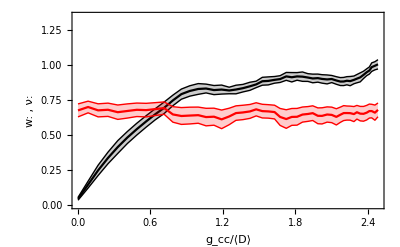

```mathematica
pbrody=Show[{pbrody1,nuplot1(*,ListPlot[histnufittable,PlotStyle->Red]*)},PlotRange->{0,1.35},FrameLabel->{"g_cc/⟨D⟩","w: , ν: "}]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pbrody.pdf",pbrody]
```

~/Code/Nchannel/Square/CODES/plots/pbrody.pdf

```mathematica
yrange={0,1.15};
```

```mathematica
impad1={{80,10},{95,5}};imagewidth=400;options1={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{imagewidth,300},ImagePadding->impad1,FrameTicksStyle->{None,Automatic},AspectRatio->Full};
```

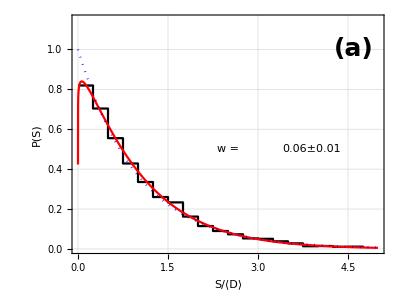

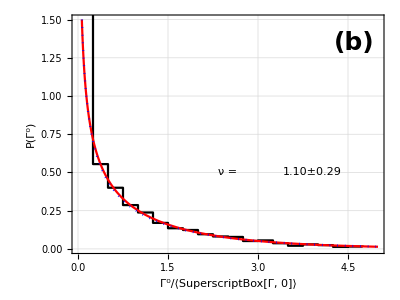

```mathematica
ic=1;
ppoisson=Show[ListPlot[sbnorm[[ic]],FrameLabel->{TraditionalForm[S/⟨D⟩],TraditionalForm[P[S]]},options1,InterpolationOrder->0,Joined->True,PlotStyle->Black],Plot[{PBrody[x,SD[[ic,7]]],PBrody[x,0.00000001]},{x,0,5},PlotStyle->{{Red},{Blue,Dotted}}],options1,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[brodyfiterror[[ic]],{2,2}],Large],{3.9,0.5}],Text[Style["(a)",25,Bold],{4.6,1}]},PlotRangeClipping->False]

ppt1=Show[ListPlot[NormalizedWidthHistTemp[[ic]],FrameLabel->{"Γ^0/⟨SuperscriptBox[Γ, 0]⟩","P(Γ^0)"},PlotRange->{0,5},options1,
Joined->True,InterpolationOrder->0,PlotRange->{0,1.5},Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic],Plot[{genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],genpt[γ,1.0]},{γ,0,5},PlotRange->{0,1.5},PlotStyle->{{Red},{Blue,Dotted}}],PlotRange->{0,1.5},
ImageSize->{imagewidth,300},
ImagePadding->impad1,
AspectRatio->Full,
Epilog->{Text[Style["ν = ",Large],{2.5,0.5}],Text[Style[NumberForm[ν/.Widthnlm[[ic]]["BestFitParameters"],{2,2}]±NumberForm[Widthnlm[[ic]]["ParameterErrors"][[1]],{2,2}],Large],{3.9,0.5}],Text[Style["(b)",25,Bold],{4.6,1.35}]}
]
```

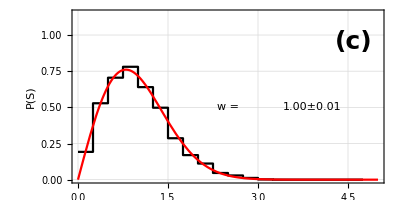

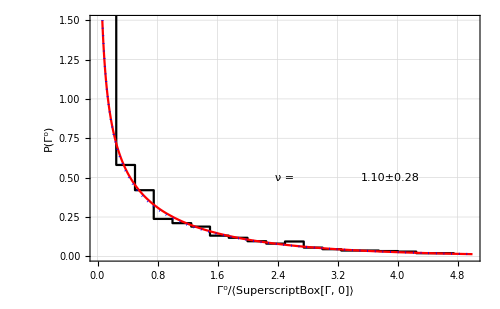

```mathematica
ic=50;
impad2={{80,10},{7,2}};
options={PlotRange->{All,yrange},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{imagewidth,200},ImagePadding->impad2,FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},AspectRatio->Full};
pwigner=Show[ListPlot[sbnorm[[ic]],options1,InterpolationOrder->0,FrameLabel->{None,TraditionalForm[P[S]]},Joined->True,PlotStyle->Black],Plot[PBrody[x,SD[[ic,7]]],{x,0,5},PlotStyle->Red],options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}],Text[Style["(c)",25,Bold],{4.6,.95}]},PlotRangeClipping->False]
ppt50=Show[ListPlot[NormalizedWidthHistTemp[[ic]],FrameLabel->{"Γ^0/⟨SuperscriptBox[Γ, 0]⟩","P(Γ^0)"},PlotRange->{0,5},Frame->True,GridLines->Automatic,LabelStyle->Large,ImageSize->{500,500/1.6},
Joined->True,InterpolationOrder->0,PlotRange->{0,1.5},Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic],Plot[{genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],genpt[γ,1.0]},{γ,0,5},PlotRange->{0,1.5},PlotStyle->{{Red},{Blue,Dotted}}],PlotRange->{0,1.5},
(*FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},*)
Epilog->{Text[Style["ν = ",Large],{2.5,0.5}],Text[Style[NumberForm[ν/.Widthnlm[[ic]]["BestFitParameters"],{2,2}]±NumberForm[Widthnlm[[ic]]["ParameterErrors"][[1]],{2,2}],Large],{3.9,0.5}](*,*)(*Text[Style["(b)",25,Bold],{4.6,1.35}]*)}
]
```

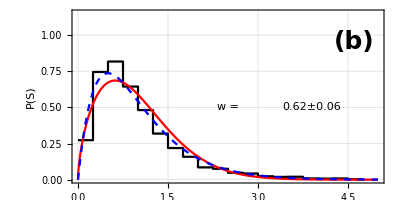

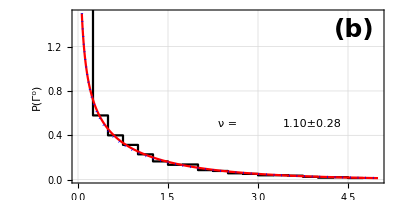

```mathematica
ic=8;
pmiddle=Show[{ListPlot[sbnorm[[ic]],options,InterpolationOrder->0,Joined->True,PlotStyle->Black,FrameLabel->{None,TraditionalForm[P[S]]}],Plot[PBrody[x,SD[[ic,7]]],{x,0,5},PlotStyle->Red],Plot[4 s Exp[-2 s],{s,0,5},PlotStyle->{Blue,Dashed}]},options,Epilog->{Text[Style["w = ",Large],{2.5,0.5}],Text[Style[NumberForm[SD[[ic,7]],{2,2}]±NumberForm[SD[[ic,8]],{2,2}],Large],{3.9,0.5}],(*Text[Style["SE_SP = ",Large],{3.0,0.3}],Text[Style[NumberForm[FitError[SemiPoisson,pfit,Null],{2,2}],Large],{3.9,0.3}]*),
Text[Style["(b)",25,Bold],{4.6,.95}]},PlotRangeClipping->False]
pptmid=Show[ListPlot[NormalizedWidthHistTemp[[ic]],FrameLabel->{None,"P(Γ^0)"},PlotRange->{0,5},options,
Joined->True,InterpolationOrder->0,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic],Plot[{genpt[γ,ν/.Widthnlm[[ic]]["BestFitParameters"]],genpt[γ,1.0]},{γ,0,5},PlotRange->{0,1.5},PlotStyle->{{Red},{Blue,Dotted}}],PlotRange->{0,1.5},FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["ν = ",Large],{2.5,0.5}],Text[Style[NumberForm[ν/.Widthnlm[[ic]]["BestFitParameters"],{2,2}]±NumberForm[Widthnlm[[ic]]["ParameterErrors"][[1]],{2,2}],Large],{3.9,0.5}],Text[Style["(b)",25,Bold],{4.6,1.35}]}]
```

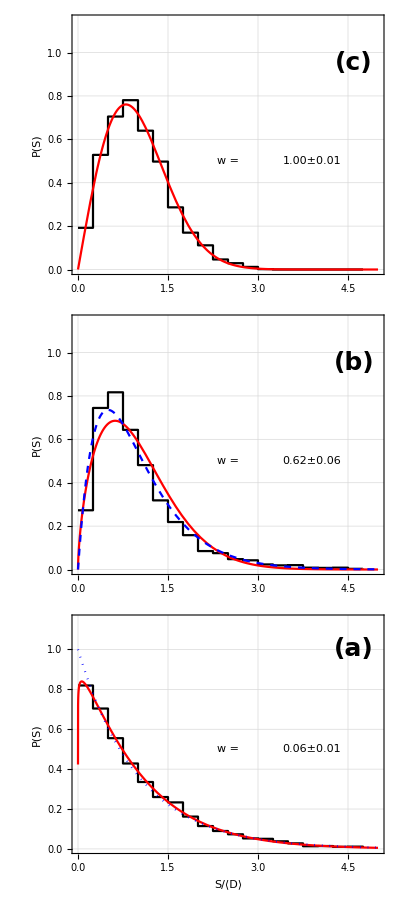

```mathematica
pstats=Grid[{{pwigner},{pmiddle},{ppoisson}},Spacings->0]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pstats.pdf",pstats]
```

~/Code/Nchannel/Square/CODES/plots/pstats.pdf

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/pporterthomas.pdf",ppt50]
```

~/Code/Nchannel/Square/CODES/plots/pporterthomas.pdf

```mathematica
w/.nlmbrody[[1]]["BestFitParameters"]
```

0.0565872

```mathematica
Normalize[[1]]
```

{0.125,1.5437}

```mathematica
ChiSqr[genpt,WidthFitHist[[1]],1.0]
```

1.

0.26821

```mathematica
(Widthnlm[[1]]["EstimatedVariance"])^2
```

0.000132908

```mathematica
WidthArrayTemp=Table[Table[DataArray[[ic]][[i,7]],{i,1,nw[[ic]]}],{ic,1,Length[PSD]}];
MeanWidth=Table[Mean[WidthArrayTemp[[ic]]],{ic,1,Length[PSD]}];
ScaledWidthArray=Table[WidthArrayTemp[[ic]]/MeanWidth[[ic]],{ic,1,Length[PSD]}];
WidthCountsTemp=Table[BinCounts[ScaledWidthArray[[ic]],{bins}],{ic,1,Length[PSD]}];
```

```mathematica
WidthHistograms=Table[Table[{(bins[[i]]+bins[[i+1]])/2,WidthCountsTemp[[ic,i]]},{i,1,Length[bins]-1}],{ic,1,Length[PSD]}];
```

```mathematica
NormalizedWidthHistTemp[[1]]
```

{{0.,1.57257},{0.25,0.554782},{0.5,0.400103},{0.75,0.286672},{1.,0.238206},{1.25,0.170147},{1.5,0.135086},{1.75,0.123743},{2.,0.095901},{2.25,0.0814643},{2.5,0.0783707},{2.75,0.0515597},{3.,0.0556845},{3.25,0.037123},{3.5,0.0206239},{3.75,0.0299046},{4.,0.0247486},{4.25,0.0134055},{4.5,0.0154679},{4.75,0.0144367}}

```mathematica
Total[(Widthnlm[[ic]]["FitResiduals"])^2]
```

0.242862

```mathematica
NormalizedWidthHistTemp[[1]]
```

{{0.,1.57257},{0.25,0.554782},{0.5,0.400103},{0.75,0.286672},{1.,0.238206},{1.25,0.170147},{1.5,0.135086},{1.75,0.123743},{2.,0.095901},{2.25,0.0814643},{2.5,0.0783707},{2.75,0.0515597},{3.,0.0556845},{3.25,0.037123},{3.5,0.0206239},{3.75,0.0299046},{4.,0.0247486},{4.25,0.0134055},{4.5,0.0154679},{4.75,0.0144367}}

```mathematica
ResidualSum[genpt,NormalizedWidthHistTemp[[ic]],ν/.Widthnlm[[ic]]["BestFitParameters"]]
```

ComplexInfinity

```mathematica
chi2widths=Table[
{SD[[ic,5]],RedChiSqr[genpt,WidthHistograms[[ic]],ν/.Widthnlm[[ic]]["BestFitParameters"]]},{ic,1,50}]
```

{{0.0040909,13.4345},{0.087476,12.554},{0.17015,14.1088},{0.25192,15.0378},{0.3326,13.7891},{0.41224,12.8976},{0.48993,12.7384},{0.56708,12.1746},{0.6418,12.9953},{0.71583,13.5941},{0.78805,14.0216},{0.85805,14.7977},{0.92742,15.699},{0.99716,15.5416},{1.0619,15.327},{1.1274,15.8037},{1.1906,15.8513},{1.2529,16.2303},{1.309,15.8542},{1.3665,14.6667},{1.4244,14.7636},{1.4759,14.0868},{1.5267,13.574},{1.5756,13.3236},{1.6278,13.3229},{1.6735,12.7391},{1.7243,12.3142},{1.7701,12.3972},{1.8136,11.6566},{1.8584,11.6296},{1.9032,11.3272},{1.9432,10.6937},{1.9854,10.5449},{2.02,11.4607},{2.0619,11.7575},{2.1001,11.4181},{2.1382,10.5715},{2.1713,10.1098},{2.1987,9.40889},{2.2251,9.94798},{2.2524,9.52738},{2.2835,9.83739},{2.308,9.52409},{2.3351,9.88009},{2.3625,9.1708},{2.3888,8.41475},{2.4108,7.65629},{2.4302,6.82624},{2.4568,7.21699},{2.4822,7.85341}}

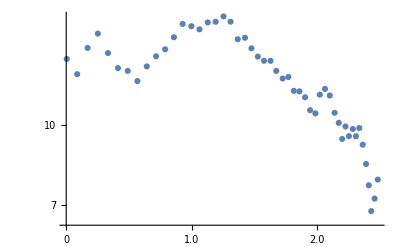

```mathematica
ListLogPlot[chi2widths,Ticks->All]
```

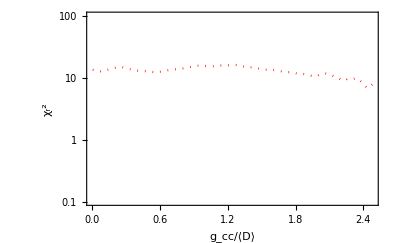

```mathematica
pwidthptchisqr=ListLogPlot[chi2widths,PlotRange->{0.1,100},FrameTicks->{{All,None},{All,None}},Frame->True,PlotStyle->{Red,Dotted},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ_r^2"}]
(*pwidthptchisqr=ListPlot[Table[
{SD[[ic,5]](*w/.nlmbrody[[ic]]["BestFitParameters"]*),Total[(Widthnlm[[ic]]["FitResiduals"])^2]},{ic,1,50}],Frame->True,PlotStyle->{Red,Dotted},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ^2"},GridLines->None,Axes->False]*)
```

```mathematica
LSdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.400","Table"];(*Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];*)
LS=DeleteCases[LSdat,LSdat[[1]]];
Length[LS]
50
LSBC=Table[Table[{bins[[i]],LS[[ic,i+8]]},{i,1,20}],{ic,1,Length[LS]}];
LSHistogramFit=Table[Table[{(bins[[i]]+bins[[i+1]])/2,LSBC[[ic,i,2]]},{i,1,Length[bins]-1}],{ic,1,Length[LS]}];
```

50

50

```mathematica
Total[(nlmbrody[[ic]]["FitResiduals"])^2]
```

0.0602246

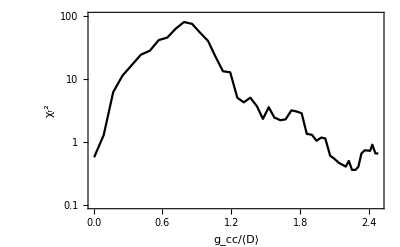

~/Code/Nchannel/Square/CODES/plots/SemiPoisson-ChiSqr.pdf

```mathematica
pbrodychisqr=ListLogPlot[Table[
{SD[[ic,5]],RedChiSqr[PBrody,LSHistogramFit[[ic]],w/.nlmbrody[[ic]]["BestFitParameters"]]},{ic,1,50}],PlotRange->{0.1,100},FrameTicks->{{All,None},{All,None}},Frame->True,PlotStyle->Black,Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ_r^2"},GridLines->None,PlotRange->All]
(*pbrodychisqr=ListPlot[Table[
{SD[[ic,5]],Total[(nlmbrody[[ic]]["FitResiduals"])^2]},{ic,1,50}],Frame->True,PlotStyle->Black,Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ^2"},GridLines->None,PlotRange->All]*)
```

```mathematica
WidthHistograms[[1]]
```

{{0.125,1525},{0.375,538},{0.625,388},{0.875,278},{1.125,231},{1.375,165},{1.625,131},{1.875,120},{2.125,93},{2.375,79},{2.625,76},{2.875,50},{3.125,54},{3.375,36},{3.625,20},{3.875,29},{4.125,24},{4.375,13},{4.625,15},{4.875,14}}

{{0.,0.81961},{0.25,0.704},{0.5,0.55535},{0.75,0.42839},{1.,0.33548},{1.25,0.26013},{1.5,0.23329},{1.75,0.16206},{2.,0.11458},{2.25,0.089806},{2.5,0.07329},{2.75,0.052645},{3.,0.050581},{3.25,0.038194},{3.5,0.027871},{3.75,0.013419},{4.,0.014452},{4.25,0.010323},{4.5,0.011355},{4.75,0.0051613}}

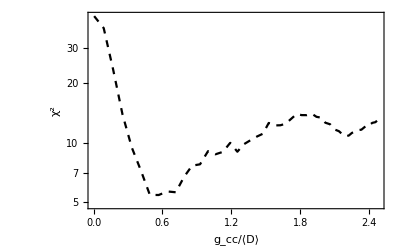

```mathematica
pspchisqr=ListLogPlot[Table[
{SD[[ic,5]](*w/.nlmbrody[[ic]]["BestFitParameters"]*),RedChiSqr[SemiPoisson,LSHistogramFit[[ic]],Null]},{ic,1,50}],Frame->True,PlotStyle->{Black,Dashed},Joined->True,LabelStyle->Large,FrameLabel->{"g_cc/⟨D⟩","χ^2"},GridLines->None,FrameTicks->{{All,None},{All,None}}]
```

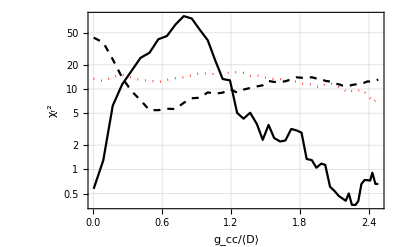

```mathematica
pchisqr=Show[{pwidthptchisqr,pspchisqr,pbrodychisqr},PlotRange->All,GridLines->Automatic]
```

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/ChiSqrPlot.pdf",pchisqr]
```

~/Code/Nchannel/Square/CODES/plots/ChiSqrPlot.pdf

```mathematica
Table[{pfitbins[[i]],Posdata[[ic,i+8]]},{i,1,20}]
```

{{0.125,0.25689},{0.375,0.69896},{0.625,0.80171},{0.875,0.68397},{1.125,0.50629},{1.375,0.32968},{1.625,0.2494},{1.875,0.14985},{2.125,0.099545},{2.375,0.052448},{2.625,0.058871},{2.875,0.025689},{3.125,0.025689},{3.375,0.020337},{3.625,0.012845},{3.875,0.0064223},{4.125,0.0096334},{4.375,0.0032111},{4.625,0.0053519},{4.875,0.0032111}}

```mathematica
ic=9;FitError[PBrody,Table[{pfitbins[[i]],Posdata[[ic,i+8]]},{i,1,20}],SD[[ic,7]]]
```

0.0479372

```mathematica
ic=9;FitError[SemiPoisson,Table[{pfitbins[[i]],Posdata[[ic,i+8]]},{i,1,20}],Null]
```

0.0425943

~/Code/Nchannel/Square/CODES/plots/pstats.pdf

### Width data...

```mathematica
avgwidths=Table[{PSD[[i,5]],PSD[[i,6]]PSD[[i,3]]},{i,1,Length[PSD]}];
```

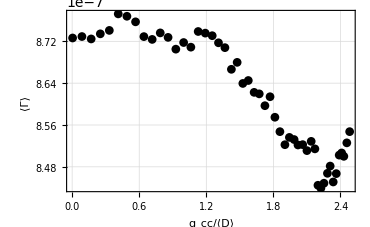

```mathematica
ListPlot[avgwidths,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic,PlotRange->All,Joined->False,PlotMarkers->Automatic,FrameLabel->{"g_cc/⟨D⟩","⟨Γ⟩"}]
```

```mathematica
avgwidths2=Table[{PSD[[i,4]],PSD[[i,6]]},{i,1,Length[PSD]}];
```

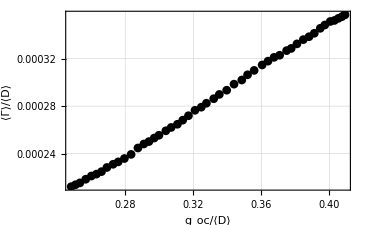

```mathematica
ListPlot[avgwidths2,Frame->True,PlotStyle->Black,LabelStyle->Large,GridLines->Automatic,PlotRange->All,Joined->False,PlotMarkers->Automatic,FrameLabel->{"g_oc/⟨D⟩","⟨Γ⟩/⟨D⟩"}]
```

```mathematica
MeanW[ic_,E1_,E2_]:=Module[{WidthData,i,nw,w},
WidthData=DataSelect[ic,E1,E2];(*Select[AWDTrimmed,(#1[[3]]==ic && EE<#1[[5]]<EE+WindowE)&];*)
nw=Length[WidthData];
w=Table[WidthData[[i,7]],{i,1,nw}];
{Mean[w],StandardDeviation[w],nw}
]
```

```mathematica
ic=10;
mw=MeanW[1,0,0.1];mw[[2]]/√mw[[3]]
```

0.

```mathematica
w1=ErrorListPlot[Table[t=MeanW[Emin,Emax,ic];{{SD[[ic,4]],t[[1]]/SD[[ic,3]] },ErrorBar[(t[[2]]/√t[[3]])]},{ic,1,Length[SD]}],Joined->False,PlotStyle->Black,Frame->True,PlotRange->All,FrameLabel->{"g_oc/⟨D⟩","⟨Γ⟩/⟨D⟩"},LabelStyle->{Large}]
```

StandardDeviation::shlen: The argument {} should have at least two elements.

Power::infy: Infinite expression 1/0 encountered.

StandardDeviation::shlen: The argument {} should have at least two elements.

Power::infy: Infinite expression 1/0 encountered.

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
w2=ErrorListPlot[Table[t=MeanW[Emin,Emax,ic];{{SD[[ic,4]],t[[1]]/SD[[ic,3]]},ErrorBar[t[[2]]/√t[[3]]]},{ic,1,Length[SD]}],Joined->False,PlotStyle->Black,Frame->True,PlotRange->All,FrameLabel->{{"⟨Γ⟩/⟨D⟩",None},{None,"g_oc/⟨D⟩"}},Ticks->{{Automatic,Automatic},{None,Automatic}},LabelStyle->{Large}]
```

StandardDeviation::shlen: The argument {} should have at least two elements.

Power::infy: Infinite expression 1/0 encountered.

StandardDeviation::shlen: The argument {} should have at least two elements.

Power::infy: Infinite expression 1/0 encountered.

StandardDeviation::shlen: The argument {} should have at least two elements.

General::stop: Further output of StandardDeviation::shlen will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

$Aborted

### Number variance of resonances

```mathematica
AllWidthData=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.800","Table"];
(*AllWidthData=Import["~/Code/Nchannel/Square/CODES/fort.800","Table"];*)
```

```mathematica
AWD=DeleteCases[DeleteCases[AllWidthData,AllWidthData[[1]]],{}];
```

```mathematica
Sdat=Import["~/Code/Nchannel/Square/CODES/resdata_from_morgoth/fort.700","Table"];
(*Sdat=Import["~/Code/Nchannel/Square/CODES/fort.700","Table"];*)
SD=DeleteCases[Sdat,Sdat[[1]]];
```

```mathematica
ic=50;iens=2;
DataKeep=Select[AWD,(#1[[3]]==ic && #1[[2]]==iens)&];
nw=Length[DataKeep]
```

24

```mathematica
rpos=Table[DataKeep[[i,5]],{i,1,nw}]
```

{0.0025048,0.0044937,0.013442,0.018354,0.01974,0.022861,0.027451,0.028615,0.031919,0.038395,0.040348,0.049826,0.053422,0.057946,0.060167,0.065107,0.070435,0.074552,0.078588,0.082017,0.08484,0.089559,0.092336,0.094748}

```mathematica
tab1=Table[{DataKeep[[i,5]],i-1},{i,1,nw}];
f1=Interpolation[tab1,InterpolationOrder->0]
```

InterpolatingFunction[{{0.0025048, 0.094748}}, <>]

```mathematica
rpos
```

{0.0025048,0.0044937,0.013442,0.018354,0.01974,0.022861,0.027451,0.028615,0.031919,0.038395,0.040348,0.049826,0.053422,0.057946,0.060167,0.065107,0.070435,0.074552,0.078588,0.082017,0.08484,0.089559,0.092336,0.094748}

0.1

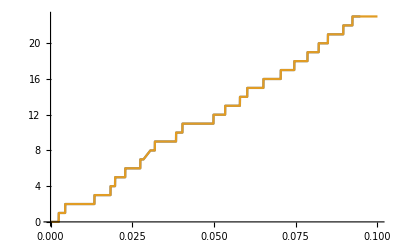

```mathematica
Emin=0.0;Emax=0.1
Plot[{(i=FirstPosition[rpos,u_/;u>EE,0][[1]];i-1),f1[EE]},{EE,Emin,Emax}]
```

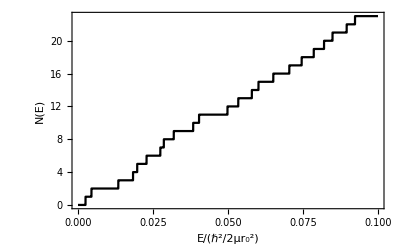

```mathematica
Plot[f1[EE],{EE,Emin,Emax},Frame->True,LabelStyle->Large,PlotStyle->Black,FrameLabel->{"E/(ℏ^2/2μr_0^2)","N(E)"},PlotPoints->100]
```

```mathematica
DataKeep=Select[AWD,(#1[[3]]==ic && #1[[2]]==iens)&];
```

```mathematica
NETable=Table[
DataKeep=Select[AWD,(#1[[3]]==ic && #1[[2]]==iens)&];nw=Length[DataKeep];Table[{DataKeep[[i,5]],i-1},{i,1,nw}],
{ic,1,Length[SD]},{iens,1,NumEns}];
```

```mathematica
NumEns=100;
fall=Table[
Interpolation[NETable[[ic,iens]],InterpolationOrder->0],{ic,1,Length[SD]},{iens,1,NumEns}];
```

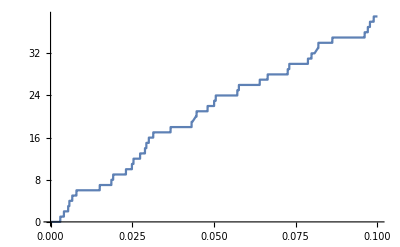

```mathematica
Plot[fall[[2,3]][Energy],{Energy,Emin,Emax},PlotPoints->100]
```

```mathematica
0.1/0.004/4
```

6.25

```mathematica
NERange[ΔE_,E0_,ic_,iens_]:=fall[[ic,iens]][E0+ΔE]-fall[[ic,iens]][E0]
```

```mathematica
Plot[NERange[ΔE,0.,1,1],{ΔE,Emin,Emax},PlotPoints->100]
```

```mathematica
NumEns=100;
Emin=0.0;Emax=0.1;NumWindows=Table[(Emax-Emin)/SD[[ic,3]]/3,{ic,1,Length[SD]}]
```

{13.6361,13.6333,13.5766,13.5084,13.43,13.3494,13.2422,13.1529,13.0366,12.9334,12.8215,12.697,12.5843,12.4938,12.3576,12.2477,12.1296,12.0146,11.8582,11.7288,11.616,11.4638,11.3205,11.1763,11.0661,10.9229,10.8225,10.6992,10.5713,10.4595,10.3552,10.2328,10.1283,9.9932,9.90089,9.79672,9.69782,9.58185,9.44769,9.31645,9.19515,9.09504,8.97408,8.86831,8.76893,8.66972,8.5593,8.44502,8.35967,8.27397}

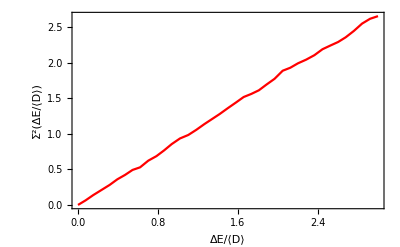

```mathematica
ΔEmax=(Emax-Emin)/13;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2c1=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{1}}]],
{DEOverD,0,3},PlotPoints->20,MaxRecursion->1,
PlotStyle->{{Red},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨D⟩","Σ^2(ΔE/⟨D⟩)"}]
```

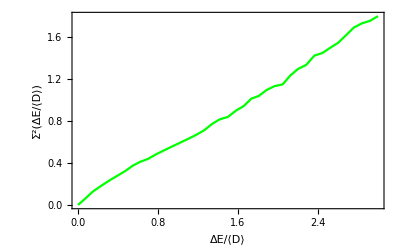

```mathematica
ΔEmax=(Emax-Emin)/10;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2cmid=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{8}}]],
{DEOverD,0,3},PlotPoints->20,MaxRecursion->1,
PlotStyle->{{Green},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨D⟩","Σ^2(ΔE/⟨D⟩)"}]
```

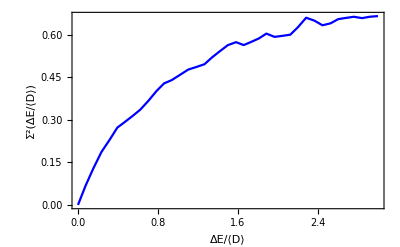

```mathematica
ΔEmax=(Emax-Emin)/6;
Erange=Table[EE,{EE,Emin,Emax,ΔEmax}];
nerange=Length[Erange]-1;
psigma2cwigner=Plot[Evaluate[Table[(
Sum[(NERange[DE,Erange[[ie]],ic,iens])^2,{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange)
-(Sum[NERange[DE,Erange[[ie]],ic,iens],{iens,1,NumEns},{ie,1,nerange}]/(NumEns*nerange))^2)/.DE->DEOverD SD[[ic,3]],
{ic,{50}}]],
{DEOverD,0,3},PlotPoints->20,MaxRecursion->1,
PlotStyle->{{Blue},{Green},{Blue}},
Frame->True,
LabelStyle->Large,
FrameLabel->{"ΔE/⟨D⟩","Σ^2(ΔE/⟨D⟩)"}]
```

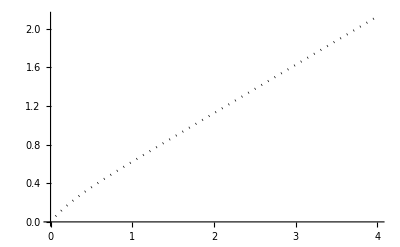

```mathematica
pSP=Plot[L/2+(1-Exp[-4 L])/8,{L,0,4},PlotStyle->{Black,Dotted}]
```

```mathematica
N[EulerGamma]
```

0.577216

```mathematica
Sig2Formula[β_,r_]:=2/(β π^2)(Log[β π r]+EulerGamma+1-Cos[β π r]-CosIntegral[β π r]) + r(1-2/π SinIntegral[β π r])
```

```mathematica
Sig2GOE[r_]:=2 Sig2Formula[2.0,r]+(SinIntegral[π r]/π)^2-1/π SinIntegral[π r]
```

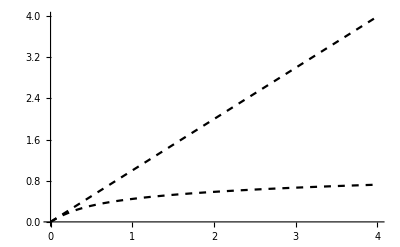

```mathematica
psigendcases=Plot[{Sig2Formula[0.001,r],Sig2GOE[r]},{r,0,4},PlotStyle->{{Black,Dashed},{Black,Dashed}}]
```

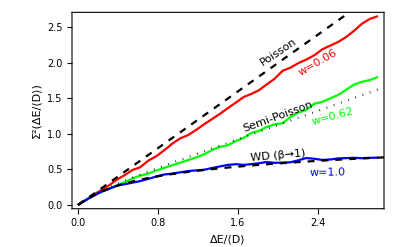

```mathematica
psig2=Show[psigma2c1,psigma2cmid,psigma2cwigner,pSP,psigendcases,
Epilog->{
Text[Style[Rotate["Poisson",34 Degree],Medium],{2.0,2.15}],
Text[Style[Rotate["Semi-Poisson",20 Degree],Medium],{2.0,1.25}],
Text[Style[Rotate["WD (β→1)",5 Degree],Medium],{2.0,0.7}],
Text[Style[Rotate["w=0.06",30 Degree],{Medium,Red}],{2.4,2.0}],
Text[Style[Rotate["w=0.62",15 Degree],{Medium,Green}],{2.55,1.25}],
Text[Style[Rotate["w=1.0",1 Degree],{Medium,Blue}],{2.5,.45}]}]
```

```mathematica
Length[DataKeep]
```

25

```mathematica
Export["~/Code/Nchannel/Square/CODES/plots/psigma2.pdf",psig2]
```

~/Code/Nchannel/Square/CODES/plots/psigma2.pdf

### What to expect for semi-poisson?

```mathematica
PBrody[x_,w_]:=(1+w)(Gamma[(2+w)/(1+w)])^(1+w)x^w Exp[-(Gamma[(2+w)/(1+w)]x)^(1+w)];
BrodyDistribution=ProbabilityDistribution[PBrody[x,w],{x,0,∞},Assumptions->w>0]
FitError[func_,list_,p_]:=Module[{tab1,nbin},
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}];
If[p==Null,
tab1=Table[(list[[i,2]]-func[list[[i,1]]])^2,{i,1,Length[list]}],
tab1=Table[(list[[i,2]]-func[list[[i,1]],p])^2,{i,1,Length[list]}]
];
nbin=Length[tab1];
√(Total[tab1]/(nbin-1))
]
SemiPoisson[s_]:=4 s Exp[-2 s]
porterthomas[x_]:=Exp[-x/2]/(√(2π x))
genpt[x_,ν_]:=(ν/2 x)^(ν/2-1)/Gamma[ν/2] ν/2 Exp[-ν/2 x]
GenPTDistribution=ProbabilityDistribution[genpt[x,ν],{x,0,∞},Assumptions->ν>0]
```

ProbabilityDistribution[x^w ⅇ^(-(x Gamma[(2+w)/(1+w)])^(1+w)) (1+w) Gamma[(2+w)/(1+w)]^(1+w),{x,0,∞},Assumptions→w>0]

ProbabilityDistribution[(2^(-ν/2) ⅇ^(-(x ν)/2) ν (x ν)^(-1+ν/2))/Gamma[ν/2],{x,0,∞},Assumptions→ν>0]

If we sample the semi-poisson distribution, what Brody parameter do we expect, and with what standard error?

```mathematica
cumsp[s_]:=Integrate[4s Exp[-2s],{s,0,s}]
```

```mathematica
cumsp[s]
```

ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s)

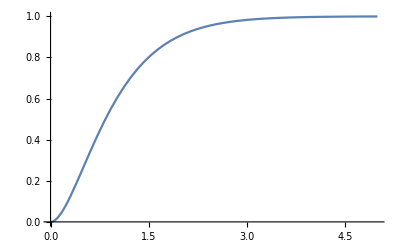

```mathematica
Plot[ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0,5}]
```

```mathematica
spacing[u_]:=s/.FindRoot[u==ⅇ^(-2 s) (-1+ⅇ^(2 s)-2 s),{s,0.5},PrecisionGoal->20][[1]]
```

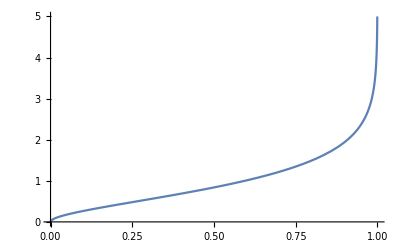

```mathematica
Plot[spacing[u],{u,0,1},PlotRange->{0,5}]
```

```mathematica
spacing[.9999]
```

5.87819

```mathematica
SPSample[n_]:=Module[{u,z},u=RandomReal[{0,0.9999999},n];Map[spacing,u]]
```

```mathematica
w0=0.74;
NP=1000;
dx=0.2;
Bins=Table[t,{t,0,5,dx}];
samp=SPSample[NP];
```

```mathematica
ChiSqr[func_,hist_,p_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=hist[[2,1]]-hist[[1,1]];
Ntot=Total[hist[[All,2]]];
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]],p])^2/(Ntot dbin  func[hist[[i,1]],p]),{i,1,Length[hist]}];
Print[p];
If[p== Null,
tab1=Table[(hist[[i,2]]-Ntot  dbin func[hist[[i,1]]])^2/(Ntot dbin  func[hist[[i,1]]]),{i,1,Length[hist]}]
];
nbin=Length[hist];
Total[tab1]
]
```

```mathematica
Var[func_,P_]:=Module[{tab1,nbin,dbin,Ntot},
dbin=P[[2,1]]-P[[1,1]];
Ntot=Total[P[[All,2]]];
tab1=Table[0,{i,1,Length[P]}];
tab1=Table[(P[[i,2]]-func[P[[i,1]]])^2,{i,1,Length[P]}];

nbin=Length[P];
1/(nbin-1)Total[tab1]
]
```

```mathematica
bc=BinCounts[samp,{Bins}];
bcnorm=bc/NP/dx;
bnorm=Table[{(Bins[[i]]),bcnorm[[i]]},{i,1,Length[Bins]-1}];
bcfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bc[[i]]},{i,1,Length[Bins]-1}];
bfit=Table[{(Bins[[i]]+Bins[[i+1]])/2,bcnorm[[i]]},{i,1,Length[Bins]-1}];
```

```mathematica
ChiSqr[SemiPoisson,bcfit,Null]
```

Null

19.5923

```mathematica
ChiSqr[PBrody,bcfit,0.53]
```

0.53

45.1339

```mathematica
Var[SemiPoisson,bfit]
```

0.00106352

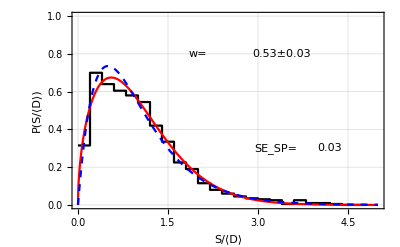

```mathematica
ph=ListPlot[bnorm,InterpolationOrder->0,Joined->True,PlotStyle->Black];
psp=Plot[4s Exp[-2s],{s,0,5},PlotStyle->{Blue,Dashed}];
nlm=NonlinearModelFit[bfit,{PBrody[z,w]},{{w,w0}},z,Method->"LevenbergMarquardt",ConfidenceLevel->0.9999];
pb=Plot[PBrody[z,w/.nlm["BestFitParameters"]],{z,0,5},PlotStyle->{Red}];
Show[{ph,pb,psp},PlotRange->{0,1},Frame->True,GridLines->Automatic,FrameLabel->{"S/⟨D⟩","P(S/⟨D⟩)"},LabelStyle->Large,Epilog->{
Text[Style["SE_SP= ",Large],{3.3,0.3}],
Text[Style["w=",Large],{2,0.8}],
Text[Style[NumberForm[FitError[SemiPoisson,bfit,Null],{2,2}],Large],{4.2,0.3}],Text[Style[NumberForm[w/.nlm["BestFitParameters"],{2,2}]±NumberForm[FitError[PBrody,bfit,w/.nlm["BestFitParameters"]],{2,2}],Large],{3.4,0.8}]}]
```